# Fit vertex angles in stationary patterns from 6 simulations, measure domain sizes, and the number of vertices (corners) of each domain (same simulations then also used for von-Neumann statistics)

## Setup

### Load format specifiers to import Comsol data

```mathematica
NotebookEvaluate[ParentDirectory[NotebookDirectory[]]<>"/vonNeumannStats/Comsol2Mathematica2hdf5.nb",
InsertResults->False,
EvaluationElements->Automatic
];
```

## Import data

```mathematica
times=Join[{0},10^Range[0,5.6,0.1]];
```

```mathematica
dataE=Import[ParentDirectory[NotebookDirectory[]]<>"/vonNeumannStats/MinSwitchPMB-2Dflat-MinEmesh-vonNeumann1.txt","Comsol2DSweep"];
data=dataE["mde+me"][[{1,Length[times]+1}]];
```

```mathematica
dataE=Import[ParentDirectory[NotebookDirectory[]]<>"/vonNeumannStats/MinSwitchPMB-2Dflat-MinEmesh-vonNeumann2.txt","Comsol2DSweep"];
data=Join[data,dataE["mde+me"][[{1,Length[times]+1}]]];
```

```mathematica
dataE=Import[ParentDirectory[NotebookDirectory[]]<>"/vonNeumannStats/MinSwitchPMB-2Dflat-MinEmesh-vonNeumann3.txt","Comsol2DSweep"];
data=Join[data,dataE["mde+me"][[{1,Length[times]+1}]]];
```

MinD density for example plot

```mathematica
dataD=Import[ParentDirectory[NotebookDirectory[]]<>"/vonNeumannStats/MinSwitchPMB-2Dflat-MinD-vonNeumann1.txt","Comsol2DSweep"];
dataMinD=dataD["mde+md"][[{1,Length[times]+1}]];
```

Color scheme RGB

```mathematica
colorMap={minD/1.5,minE,minE+minD/1.5/1.5};
```

## Image preparation

Skeleton of the network

```mathematica
branchIm=Table[Thinning@Binarize[Image[sim]//ImageAdjust],{sim,data}];
```

```mathematica
branchIm[[1]]
```

-Graphics-

## Analysis of triple vertices

## Find vertices

### Average branch widths

Determine average branch width by binarizing the experimental network image (cleanI) at half-maximum intensity, count the white pixels (width*length of network) and divide by the white pixels in the network skeleton (length of network because everywhere only one pixel wide)

```mathematica
width=N@Total@Flatten@Table[ImageData[Binarize[Image[sim]//ImageAdjust,0.5]],{sim,data}]/(Total@Flatten@(ImageData/@branchIm))
```

4.3851

Branch cross sections

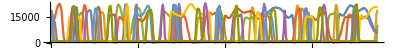

```mathematica
ListLinePlot[Transpose[data[[1]][[;;,;;;;30]]],AspectRatio->1/10,PlotRange->All]
```

### Determine branch points

The branch width is about 4 pixels, see below.
We prun branches shorter than 10 pixels because for their vertices no reliable angles can be determined.

```mathematica
branchImPrun=Pruning[#,10]&/@branchIm;
```

```mathematica
branchImPrun[[1]]
```

-Graphics-

```mathematica
branchPoints=MorphologicalBranchPoints/@branchImPrun;
```

```mathematica
branchPointCoords=ImageValuePositions[#,1]&/@branchPoints;
```

```mathematica
HighlightImage[branchImPrun[[1]],{AbsolutePointSize[3],branchPointCoords[[1]]}]
```

-Graphics-

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVertices=Table[Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@bpCoords,0.]]}]/@bpCoords,#[[-1]]>10&],{bpCoords,branchPointCoords}];
Length/@tripleVertices
```

{95,95,96,101,98,97}

### 4-fold vertices

```mathematica
quadrupleVerticesRaw=Table[Complement[branchPointCoords[[ind]],tripleVertices[[ind,All,1]]],{ind,Length@data}];
quadrupleVertices=Table[DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadVertices[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadVertices],I],{quadVertices,quadrupleVerticesRaw}];
Length/@quadrupleVertices
```

{0,0,0,0,0,0}

```mathematica
vertices=tripleVertices;
```

```mathematica
HighlightImage[branchIm[[1]],{AbsolutePointSize[5],tripleVertices[[1]]}]
```

-Graphics-

## Analysis of triple vertices

Experimental network data labeled by pixel positions

```mathematica
{dy,dx}=Dimensions@data[[1]];
```

```mathematica
dataPos=Table[{j-0.5,dy-i+0.5,#[[i,j]]},{i,1,Dimensions[#][[1]]},{j,1,Dimensions[#][[2]]}]&/@data;
```

### Measurement functions

Fit the vertex by assuming Gaussian cross-sections of the vertex arms:

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ]:=
Total[
Function[d,
(d[[3]]-Exp[-#/((width/2)^2/Log[2])])^2&@Min[If[Length@#==0,{1000},#]&@((Norm[d[[{1,2}]]-{x1,x2}]^2-((d[[{1,2}]]-{x1,x2}).{Cos[#],Sin[#]})^2)&/@
Select[angles,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle],Sin[angle]})>-10^-10]
])
]]/@vertexData[[2]]];
```

```mathematica
ClearAll@measureData;
measureData[vertexData_,armNumber_]:=
Block[
{
dataW,
iniCond,
iniCondClean,
vars,
sol,sol2,
fitSuccess=1,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[3]]}&/@Transpose[{vertexData[[2,All,1]],vertexData[[2,All,2]],Rescale@vertexData[[2,All,3]]}]);
iniCond=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.05+(HistogramList[dataW,{0,2Pi,0.2}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.2}],1,0,0,Padding->"Periodic"]));
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondClean=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCond,{#[[1]]-2Pi,#[[2]]}&/@iniCond,{#[[1]]+2Pi,#[[2]]}&/@iniCond],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCond}],#[[2]]&][[All,1]];
If[Length[iniCondClean]<3,
sol=I,
iniCond=iniCondClean[[-armNumber;;]];
vars=Symbol["a"<>ToString[#]]&/@Range[Length@iniCond];
Quiet@Check[sol=Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2];,fitSuccess=0;];
(*Try a second time if it failed*)
If[fitSuccess==0,
sol2=Check[Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];
sol=sol2;
];
];
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,Sort[If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)]];
If[Min[Abs@Differences[fit[[2;;]]]]<0.01,
I,
fit]
]
];
```

### Analysis

The fit data for each vertex is taken as the data points within a 15 pixel large radius around the branch point. If a second branch point lies closer than 15 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[dataPos[[#,Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[15,vertex[[2]]]&]},{vertex,tripleVertices[[#]]}]&/@Range[Length@data];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[1,Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data[[1]]}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw=Table[ParallelTable[measureData[data,3],{data,vertData},Method->"FinestGrained"],{vertData,vertex3Data}];
```

```mathematica
fittedVertices=Table[Select[Transpose[{Range@Length@#,#}&@vertMeas],ListQ[#[[2]]]&][[All,1]],{vertMeas,vertex3MeasurementsRaw}];(*indices of successfully fitted vertices*)
failedVertices=Table[Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],#[[2]]==I&][[All,1]],{vertMeas,vertex3MeasurementsRaw}];(*indices of vertices that couldn't be fitted*)
vertex3Measurements=Table[DeleteCases[vertMeas,I],{vertMeas,vertex3MeasurementsRaw}];(*fitted vertices*)
Length/@vertex3Data
Length/@vertex3Measurements
```

{95,95,96,101,98,97}

{95,95,96,101,98,97}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[1,fittedVertices[[1]]]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[1,Floor@i,;;2]]-(tripleVertices[[1,fittedVertices[[1]]]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[1,fittedVertices[[1]]]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[1,fittedVertices[[1]]]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[1,Floor@i]],1]]]
],{i,1,Length@vertex3Measurements[[1]]}]
```

```mathematica
Show[
HighlightImage[Image[data[[1]]]//ImageAdjust,{AbsolutePointSize[5],tripleVertices[[1]]}],
Graphics[Join[{Darker@Red,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements[[1]],1],
{RGBColor[{255,150,20}/255]}]]
]
```

-Graphics-

```mathematica
angles3=Table[(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertMeas[[All,3;;]]),{vertMeas,vertex3Measurements}];
```

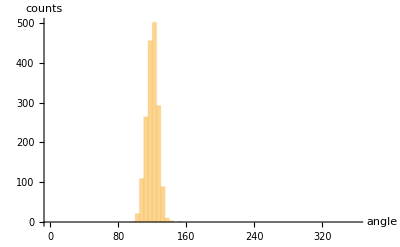

```mathematica
Histogram[{
Flatten[angles3,2]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles3,2]]
```

120.

```mathematica
StandardDeviation[Flatten[angles3,2]]
```

6.63325

#### FitList

```mathematica
vertex3MeasurementsRaw={{{126.49988051291758,293.5117950819922,-1.6256705259310102,0.5109896207787794,2.6239318478429183},{164.5168659452457,292.51475985248356,-1.4961192270708383,0.568380879464518,2.527954807229874},{82.5024169701498,278.49607484047675,-3.025312505928891,-0.8516896306464006,1.0194863273279478},{210.51347916541434,278.5002741348205,-2.3193464380216327,-0.3313562858439985,2.017872296446016},{62.48872851991755,276.4901177807364,-2.124570206451486,0.0893852164809747,2.2123218112021372},{276.5031814037459,274.5055674565553,-1.452053719871609,0.6253640047428157,2.577623064781153},{230.490389853704,271.49406931616284,-1.2594320123478766,0.6954216053550841,2.779141981554482},{123.51532465415384,266.49357929094094,-2.767840529956387,-0.5945050148638823,1.3723780432263355},{166.49630099026004,265.4930515839139,-2.6077986206180035,-0.46970536466745016,1.677087675544237},{99.4941364947868,258.5012099296472,-1.8646934038784326,0.2778842247916299,2.276879052469368},{187.49169732912966,255.5021906783299,-1.2454782642515552,0.7384157773949588,2.7112232592878307},{48.509861651107954,254.5111560894674,-3.061241017015283,-0.8968132118681186,0.9511797581202067},{26.49010890911074,253.48749314601042,-2.1657886505608244,0.020571204986312226,2.1859377361906644},{142.49305520984123,252.50076677493865,-1.6932674569897097,0.46680332508444633,2.464906283647273},{278.48585042845997,251.49678699707147,-2.5216679394879162,-0.4258132311402424,1.6365120488347544},{237.51111948474622,244.50957986378137,-2.4066621407825552,-0.323401778935115,1.7997658204707916},{258.4969023781166,236.49637598485538,-1.2399329246365505,0.6631193397414722,2.719263879627408},{193.5089644116028,234.49620982122258,-2.34264603854967,-0.22313494547764728,1.8154705850826647},{91.50791922001875,233.49916870066102,-2.9765397579668753,-0.7533149417418663,1.2372767448538546},{12.509423051417082,231.4953733686187,-0.9800109809259426,1.0105909078386361,3.1101938321450935},{66.49347724678364,229.50236023408183,-2.1498822784737075,0.16493937525764424,2.1792165165711093},{137.5126160149498,227.50374695500338,-2.8052750926260095,-0.7047784577611838,1.27709331315691},{218.4966535980066,227.50947813259214,-1.2506532500031307,0.7233202688257627,2.812032627871759},{108.49082739177254,217.50384752720956,-1.7789758600991923,0.3652699031895045,2.3715356740649978},{177.50371568656428,217.51531398661524,-1.1281360079642622,0.8155785458410263,3.1114028014471424},{150.50125677737387,215.50894042257366,-1.7512997403451718,0.17943306913289503,2.33901480315588},{266.50170895889164,210.49547125893713,-2.3521160275457875,-0.20133458583647726,1.8831053050159314},{26.496785388325854,209.48678561617825,-2.167940487181415,-0.011086620440385025,2.133180030042383},{52.4970442425929,208.50472921185136,-1.0032835168142977,0.9419369064799847,3.077792125241959},{292.5053411146874,207.4923919110366,-1.009142010139214,0.9510613290520599,3.1083513849800637},{225.51174199782398,202.50095643687476,-2.3558509962004304,-0.344456026732767,1.8218637632504475},{249.4938410411196,193.51021305051597,-1.2509444474397546,0.7806629934454451,2.7298175157094695},{104.51038033467877,191.51249929321415,-2.611861988452767,-0.48246903585459455,1.4489801106702043},{187.49909033540314,191.51058942889682,-2.449059872159433,-0.31394927079067103,1.8997005937745952},{63.50178026072859,188.50481329752546,-2.244710036289847,-0.22270154955566707,2.0178041375010176},{146.50520508722522,187.50669466092506,-2.6182185957536115,-0.5169508250117008,1.459889915082991},{206.49415845911184,184.50179084153024,-1.2368621192372422,0.7406981892250533,2.748935123845186},{87.49738761267014,180.49468514301856,-1.4602442222451038,0.6238761267014286,2.705366634528365},{128.5041834448528,176.51012307982467,-1.5559034427827108,0.5668989098790365,2.4872522806799733},{167.50898051081637,175.5055399255036,-1.3778210193360951,0.653673845333972,2.6084459742099417},{255.48722749949582,170.51286702429604,-2.485696276419002,-0.34594478862211053,1.7766174169358813},{45.49039753643319,163.49004199060164,-3.1025607357156124,-0.868016628523445,0.9410963412063416},{26.502581876270376,162.49795310710095,-2.1810027435602373,0.06102530947891002,2.0691640914993092},{276.50386149380904,161.5133055088753,-1.376434939340409,0.5733228503610622,2.671822118712586},{213.50656276320305,159.50758886298723,-2.4335982320408323,-0.3563133316806384,1.8138900695315803},{88.48881729349193,152.50678495345414,-2.6791721718861288,-0.5958308460137751,1.5480874880389388},{232.49505520608665,151.50307208472915,-1.2425016322712734,0.7167652386684743,2.6935920009383327},{171.49607056365565,150.49345813619595,-2.561851287173063,-0.427571826687673,1.7237865186337893},{127.4979781716598,149.49801781535274,-2.633403610671611,-0.4626405710378714,1.4710384977388509},{13.52028346453792,144.5163675446032,-1.0807344369151595,0.9197912303928453,3.028331096503117},{65.49617543637041,141.49116501331386,-1.7426065555117178,0.45037636806112785,2.3701056303482995},{191.5063930056949,140.5107114598729,-1.3360839050939601,0.7379355816443679,2.635509293601722},{108.5016696077099,138.5057275243796,-1.5748758739303086,0.5372814311579222,2.4981945882322916},{279.4808633039106,137.4978197823271,-2.433550496389082,-0.4732666760384942,1.6399356551984106},{150.5062265954183,136.50338438579035,-1.471578135677994,0.587089497388286,2.577447134554946},{238.4989915488535,128.50709103002467,-2.373418689004761,-0.2991255761867801,1.7683665889669482},{259.4919431170795,121.4879621568802,-1.2619990766296678,0.6546059990420041,2.795671615895859},{22.511709469920874,119.48409194202665,-2.505764938881477,-0.4857678873185484,1.8019392507470422},{62.50156160794672,118.50209584224429,-2.6235638672759114,-0.5929122601325408,1.4614499021864928},{197.50435273353597,114.50753091992729,-2.4451397253226395,-0.35725428883010263,1.821180957712736},{107.49885288424301,112.5091769260559,-2.659702757658728,-0.5517400884334485,1.496529241943722},{151.49130439469081,109.5028632468079,-2.636248058198864,-0.43595670005075876,1.5546993157695081},{43.509652014819316,107.51411329547769,-1.559852770083568,0.5256176151089705,2.5807315033758016},{216.49954862642977,107.49947936622453,-1.1417293848527623,0.7386990240460731,2.782212277040789},{87.48936426373075,101.50325150731646,-1.6552889409728275,0.5268560751560689,2.522887979437764},{130.49887998231833,97.5015003068894,-1.5746985748857454,0.5293341280687485,2.52795249671069},{175.50662010727405,96.50785613996129,-1.5759361144630062,0.6900767886558514,2.588510634848906},{266.50843622376453,96.50429097196101,-2.3497795587938652,-0.13371908028088764,1.8356311996928278},{292.51337829531315,93.51289803000961,-0.9908546173606999,0.9556831277706941,3.035922606790869},{225.50354624670575,88.50116682956124,-2.1887936687583722,-0.20950553078959783,2.0267750137068146},{252.50826202913314,82.51116428851884,-1.3101230372101549,0.7733577862126869,2.8715179691020007},{42.505309936682224,80.51140404122891,-2.642791549003514,-0.5108327155271466,1.4731310205537325},{85.49506002097574,76.5017279762019,-2.6576047977742063,-0.6374340957230875,1.4856530911272885},{128.51033171824113,70.50743705580288,-2.6488630263221338,-0.5425155729600027,1.4035625505927751},{174.49182288250304,69.50025553492178,-2.659128411994983,-0.6628060635292518,1.5002845731134915},{21.49471921916458,68.50237620112225,-1.5876032307138892,0.5417067416448078,2.54828501826521},{65.48759720844892,66.48948314428168,-1.6787250252962045,0.44241545495591733,2.5769692630062044},{212.51598612587085,63.50459901379491,-2.7829176097518897,-0.7027643333008136,1.2060104272478067},{108.50374398224136,59.50256699578198,-1.7412556927790055,0.519985910809927,2.4856457726930254},{256.50391907532753,59.49742397857683,-2.5777906258673315,-0.4097369070456081,1.6660259089833018},{149.49373596540357,56.499789089744226,-1.6462414048341465,0.4923929614101341,2.5058180448336502},{192.4936427954402,55.49505550756459,-1.7011962611680833,0.40256377569774,2.4719384822890578},{277.51304347784395,48.51847034858368,-1.5077900502610162,0.5760106089135707,2.5904173845951592},{234.4945241544803,46.495893115860234,-1.615971951387874,0.4925844772111798,2.530182023681211},{20.50312971727516,44.50076128258044,-2.5771299155402527,-0.556676407844893,1.4943352307385425},{62.51978657928061,42.509350042612596,-2.647267039592712,-0.67509499527156,1.4175605570080176},{41.49975264873559,31.508371888949412,-1.6432045238723265,0.48333533963493136,2.595101661314576},{103.4969452628707,31.51319415641785,-2.700039766281016,-0.7348722369015046,1.3415928070159637},{147.49465543622924,27.50547031821244,-2.6595633861385863,-0.5986657129424641,1.5065750442158554},{189.49895475162478,26.503238220456588,-2.62771359522452,-0.5870509132062934,1.4856755496832337},{233.49895215223992,24.513422729025354,-2.659147708542084,-0.520207510467545,1.5214578251058208},{278.4940870148351,24.510233381589586,-2.6143310909971613,-0.5139502228852328,1.5927674919238446},{84.48859746139149,23.50404594897445,-1.8572791655326264,0.35593739595577845,2.37241247756172},{123.49500604105215,14.507431010914404,-1.6538560555258224,0.5225122839228123,2.4391070544419096},{40.48443908016864,6.486386907102392,-2.6321614589658235,-0.5170263950001214,1.5536363759132432}},{{176.50406672733462,282.50244584596413,-2.8208819981323847,-0.7471580160896114,1.3580060296042928},{6.486698976678417,280.4960421643775,-2.1332471426022392,0.020318486302703238,2.0968361236432673},{29.49549574258892,280.4927977883705,-1.0617355108751236,0.936954824232756,3.12956108571396},{77.50087067340495,279.480869729589,-2.1386507784600406,-0.040955955517792984,2.1230894456036666},{257.4955721438836,279.5036387332442,-2.4381581647771076,-0.3729050877725012,1.9271112860739668},{100.50147341153439,278.5016900897012,-0.9832303388130307,0.9068780187907154,3.093818719113334},{212.51408026576672,277.5146114850474,-2.8540884207757884,-0.6783746495423993,1.2339502904208588},{152.47995807762757,276.50475196576133,-2.0717881441424413,0.18642416755239022,2.2041610623181356},{276.50207819342717,271.49385778387074,-1.40909832990144,0.6196121938868898,2.708023857575042},{189.49845982016225,270.49282205892695,-1.7153083133899076,0.30853346785621155,2.3727731299812835},{233.49532049008857,261.50592445570913,-1.5635506538132904,0.5800820534962102,2.520482038802602},{41.50603785385198,257.49686204728124,-2.332628334749538,-0.17101056124144226,2.060429931997128},{113.4911888410017,257.50639719653157,-2.2529666877275534,-0.14177542288432948,2.130349715685084},{61.502397518003114,255.49675946205747,-0.9780462766018662,0.9077008990762803,3.100493469041515},{138.51369590594396,254.5116250111735,-1.1103562488811727,0.9174486874019163,3.018495203899599},{279.486513434674,244.50366271221498,-2.5628038994522537,-0.5252914927136597,1.6545000711846358},{233.49925967719395,241.49959987748568,-2.538773128958314,-0.5310574627458559,1.5617870934412723},{72.48216454038653,239.49138203324992,-2.025504720897877,0.004369260439561158,2.1720982458868123},{187.4976070231195,239.50034230918357,-2.4890136371890375,-0.5024098705531556,1.5955749030207316},{21.495822048377256,238.50166725768983,-1.441615978699611,0.7009200113269503,2.6713616234976274},{97.5078467587856,238.51238631512038,-1.1364797823930588,0.8179260981832097,3.072784789843311},{148.49480145238235,230.49716628188685,-2.3978782767466487,-0.4026871611559523,1.9334853137285182},{255.51861639898294,228.50261797323455,-1.5124415443256407,0.6081434047861521,2.586464600486062},{211.5125916769266,226.4977762822404,-1.5224693691347102,0.6085650976177801,2.6430393299660775},{166.50805223719857,222.50385067206136,-1.3124968278973401,0.7227412256483559,2.7083558216592625},{105.50432312265869,217.50316326048195,-2.4034228487182094,-0.35524256890399014,1.8692759404504553},{23.48972892984988,216.4995093422134,-2.558331026447683,-0.5497185889369703,1.6335446699578544},{63.494341472171996,214.5142664266424,-2.7075731449955027,-0.5600541653685367,1.2994569532628841},{125.50573136180189,209.50514373471333,-1.3140184848668968,0.7452278339705921,2.7263777315250564},{43.50187171298511,204.50714471085712,-1.614417188375424,0.49240536838297616,2.612831554680036},{256.49159869304765,204.48890309853826,-2.5236751213940676,-0.46564631824428254,1.5889045796435504},{84.49982569547804,200.49434755335935,-1.437615763378575,0.6319968329462694,2.510686431522752},{213.5013408451922,199.4937427224364,-2.558824431763052,-0.43331300672170037,1.6750110517333687},{172.49143782555757,194.4825466400004,-2.4810487104617436,-0.4569922179693656,1.7781403782527618},{277.5151943989498,193.50974091691182,-1.474522500618477,0.553310565618599,2.6448636238260392},{234.50428241360038,188.50645295200056,-1.411013784876367,0.6606375936009299,2.6025233925996236},{130.4903068655337,185.50222501495705,-2.460709206417363,-0.41642059052311364,1.7369578302740436},{192.50043297199664,184.4995257925751,-1.4219498900625138,0.6535462468296315,2.669038319421035},{86.48300851997537,179.486142589282,-2.5399602922664184,-0.4882476973939404,1.6379695779486105},{42.50441658832674,177.50374657798235,-2.572776289084099,-0.5164693332172619,1.5182172035346626},{149.50514644769035,176.50200836983038,-1.3633522139203011,0.6786192700829643,2.6744414818980626},{279.504220108632,170.51061907769903,-2.459474614084566,-0.5233478058823593,1.6593548521388073},{107.50470500608797,167.51031938310052,-1.4141637900964201,0.6775381238678571,2.576840027422267},{21.508923316464706,164.51375551767006,-1.5509529770486778,0.5412062339727235,2.5921489802579045},{64.51231439120346,164.48945188372818,-1.4894464871504531,0.6096226409592225,2.571719891466657},{238.48886614699242,161.5025381772182,-2.4769274788455986,-0.4264452735581447,1.7298359180015719},{195.506169557121,157.49484764584517,-2.5373405899594004,-0.40339895075658094,1.655910230673121},{257.5008058029659,152.5045868784212,-1.1819830315972277,0.7047739400658061,2.681725324317312},{153.50536477487879,150.48957924055867,-2.4991368151824616,-0.3985018971093364,1.683397229352316},{218.51563228713778,146.4985307388252,-1.4952666054390675,0.6364196913100797,2.656233380413678},{110.49814014196058,144.4813980106942,-2.517478163541557,-0.4964478483050114,1.693005995809448},{173.5007199891354,141.4968659296459,-1.4079929350946436,0.6488564878437787,2.6950932152170344},{65.49313210964597,140.48647616156867,-2.5293419466402627,-0.4827826296778114,1.5647882071843127},{21.49089305641046,138.49810855786987,-2.624352760227413,-0.4660637086515598,1.538863156016043},{130.50870724061357,133.502790274833,-1.3831457208097224,0.6308044922837327,2.6212870153008954},{87.49526130650484,128.51779818327574,-1.4475069862273184,0.5981221436566412,2.6220261025733573},{267.48766054493666,128.48762717266467,-2.126679987317945,0.011068581202031911,2.0004972265525507},{293.5055158008263,128.48405588823655,-3.127023095579569,-1.0513700378701485,1.023221279470641},{43.5225636764724,125.49412594219963,-1.4732290507140717,0.6044081886417301,2.5220875398825533},{218.50399630794348,121.50885369881402,-2.624364370833939,-0.5364128336088702,1.4832403895623174},{177.4966842016178,115.48615894268998,-2.500994675261969,-0.43554988151288593,1.73489662462492},{133.48943942061968,108.48744664582973,-2.479233766381384,-0.42129327765361946,1.6357652776167104},{195.49891902354648,107.50165688251282,-1.3557862802713039,0.5523636297091907,2.745903620907705},{255.5078991026784,107.50724568185115,-2.9972194698600663,-0.7305902632595408,1.0728213005131222},{239.5053888469979,104.51306498597103,-1.9382896880949623,0.24383919469101142,2.332595886570526},{89.48675557843606,103.4903379897711,-2.538616810655009,-0.45684357908576756,1.6212847268730124},{44.502720502776086,101.50232070356479,-2.548436949375318,-0.5005577831684884,1.5638595656876528},{154.50622979606982,98.49783659814939,-1.3807719036675004,0.6290069894496508,2.671482837384449},{111.50128954584872,91.50948312177987,-1.4327977113324089,0.6866627804376546,2.586701827860743},{67.51264202885876,88.51923856214593,-1.489233131364698,0.5991609761694126,2.605009439345588},{22.5089708879468,87.51244208927551,-1.538519462968649,0.5445054724412013,2.6059016944089297},{277.506644815465,85.4956798435681,-1.867370327713743,0.3560147997541877,2.3395432144689408},{201.51081858418482,80.50305588752916,-2.3679637715699653,-0.15432938819857367,1.7990574178887808},{227.5100625931279,78.49355933759128,-3.1348301922811297,-0.9238772039407828,1.0557671383095182},{158.4920446456676,73.50241760118674,-2.4566919007763213,-0.4142784261038281,1.7189025730609826},{114.50041018896358,66.48525036948571,-2.5130773744810004,-0.461302073225951,1.6920663030187997},{270.51150467887214,65.49574729769319,-2.9681888411146944,-0.7779449424783833,1.1895131436108064},{68.49317406368907,63.49475410574237,-2.566410780519243,-0.445020661672144,1.5598180688879526},{22.493581696810573,62.49809999688977,-2.6146623152911235,-0.4535755844600714,1.525201132352638},{182.50401642375178,62.51126197894678,-1.3482309160313535,0.7598765935020799,2.6674837173691532},{241.5020233848118,60.507774057434816,-1.9823394794887277,0.1579316056189919,2.26391520782853},{136.50027702015942,55.50474891701838,-1.3915313465557455,0.709025081107654,2.661946961052536},{92.5014963540134,50.50623165152415,-1.452295858107645,0.6499431764298711,2.586021663367909},{46.50899571153904,49.51365696302772,-1.530828307121589,0.5585744034162956,2.608345961083977},{287.49372947977344,46.494994922054076,-2.0708101313876015,0.013869864558327229,2.2803585308236287},{185.48366515486057,43.508550285969605,-2.4144291085019645,-0.38955937150891107,1.6730812447218824},{233.4912915842035,42.5053362114264,-2.8366541060843775,-0.8513082190129783,1.1524351562212478},{207.5084127058897,32.508632146394184,-1.5878561935244904,0.45704345384924105,2.601720682114661},{141.48591908146744,29.499526738502528,-2.4141438095350245,-0.39879320975861804,1.7936513894347235},{94.49021223724877,26.49865399864743,-2.5418352238761934,-0.5319941632473789,1.6362040204430859},{46.49670748792225,25.492508172422713,-2.5825358461659613,-0.4761920283290909,1.5159552470042827},{273.52401728927794,22.508221454858063,-3.0710796337141297,-0.8866419086457152,0.9739043022966877},{161.50349921223778,21.50340928951111,-1.0964583436635689,0.7497477194296941,2.76943925338585},{251.50456561246537,20.502372328045738,-2.1468979301475106,0.1252654643190425,2.261478685806215},{206.4960495956014,6.488115166341184,-2.609366636501974,-0.4987452099651316,1.496929528996621}},{{276.52026413848444,291.50335176019547,-1.483272962101572,0.6443154841273379,2.469370211364895},{188.51493862157886,285.49474147297,-2.911716372040001,-0.702524072603587,1.3291857607473545},{163.48600649562158,280.52062731288834,-2.0902841342958487,0.1862710420401222,2.229785279939822},{24.490322229824766,278.47949119612696,-2.187560874571693,-0.052792095138414374,2.170476691236672},{113.51026720706272,278.49329412931195,-3.0935061066760223,-0.902405418708174,0.9235909121245485},{43.510368511679,277.50643119356886,-0.9335426531715074,0.9173583132572528,3.0939112426670117},{93.4924664511135,277.49434983833515,-2.188736921383417,0.05595243368809813,2.1577517531191543},{226.5172694596561,276.49869492489506,-3.1296032631060284,-0.9251104215673819,1.0015514155471321},{201.4972291126874,273.51784910005085,-1.9534327950566241,0.23738550890403393,2.323277031384471},{278.4951770158026,268.49547963441887,-2.4330531625875245,-0.4806775162764282,1.6698192268029015},{151.50306311180856,259.49684116594744,-3.028975426786958,-0.8482136994902965,1.0231430732500135},{128.48457249330485,257.4950329521465,-2.058098177720594,0.06713886470521119,2.172480773114465},{58.48567517587311,255.48502878007298,-2.2339502204251094,-0.03718969201397422,2.181531373625745},{78.49761020762844,255.49262068781468,-3.1050841315739435,-0.9896161989632932,0.9410116900739958},{240.49920682920853,254.50039658539572,-2.1959314336437625,-0.18793050702219605,2.0990089269522167},{259.49432562433407,251.49654860768482,-1.1895613340064615,0.7545248567709478,2.9884238046586615},{190.4953168905111,244.50212658044435,-2.995544167811,-0.813942907247823,1.157813232926837},{166.49960271044003,241.50269274035094,-2.006849387950473,0.10323680103660993,2.265744438117516},{115.492005303199,235.50557521768576,-3.0462097750069272,-0.8696865456526054,0.9712791001664469},{21.494186109456404,234.4942889875637,-2.3549468396479027,-0.1742382031219455,1.9670461836012247},{92.49773293224673,233.49789425682175,-2.1445679189531313,0.09696087925209636,2.130428545634098},{40.495653967245346,231.48886926797206,-1.020339319390743,0.8913718931770163,2.9887337898638147},{223.50332302423072,231.4970304889853,-0.9819071415479937,0.8897113179345264,3.133900469938821},{203.49184333650186,230.50496795775405,-2.0264763220717574,0.10627292127766978,2.3082063754947004},{270.50424253748474,225.51596188514694,-2.229061398157151,-0.09060036303918065,2.016721976116643},{292.5247639681044,223.52452580303932,-0.9597667208635374,0.9630403911420996,3.049554597724987},{155.49195587006847,217.4970539679991,-2.9895954070242032,-0.8642753470188379,1.1266107612526368},{131.48127213284522,214.49734701362814,-2.0458576986272874,0.10623776184484347,2.208927267354825},{52.497356137418194,211.48778962514186,-2.179835645984163,-0.010474738963092395,2.112312827284415},{78.51926469773747,211.4927810779169,-3.133327378254597,-0.9047663984322221,0.974422514988136},{236.49856833280506,209.49482213697829,-2.3676089992814315,-0.19543701547280984,2.1050551693666715},{255.5094673074435,206.508058219824,-1.1255985516444085,0.8762002229249907,3.015624614528501},{193.50549881128225,202.49822346097037,-2.7941964494191724,-0.5828077361246108,1.2447718994270407},{173.50336322619037,196.49197508687487,-1.953397966838261,0.24250724291766387,2.2984285650309073},{119.50513245256478,193.49701601595072,-3.0432854383849564,-0.8494579668617163,0.9932569382373035},{93.5084334922861,191.49338353463284,-2.1095718435996504,0.0635904674044053,2.229320093841497},{215.48972990176222,189.5015649673505,-1.2946546626765827,0.7115716841969255,2.658276979442301},{37.51130264294474,187.49746318761456,-3.1270890081848837,-0.88974115455308,1.0484394049992838},{8.47479868191455,186.49319425597332,-2.2153290090637805,0.03602472303774935,2.2195965084706133},{266.50004629613983,183.4844291960344,-2.2500366412413926,-0.09501590343666705,2.0322280058528555},{291.50473195182207,182.50057598365453,-3.127454090243095,-0.915602960403444,0.8707578169200826},{163.5152052919152,174.51155961990145,-3.0536238290242097,-0.8739896509392079,1.0844939950062784},{135.48919921756138,172.4926794696805,-2.0257009414823925,0.05096006955010051,2.1750432048179684},{81.50121080261647,171.4978497815604,-3.0429791090444027,-0.8673800431411732,1.0187259028620406},{221.50074441702716,169.48942489929075,-2.345145589760523,-0.2659177617558435,1.88220284150845},{53.49271093519266,167.5194007586774,-2.0596529045383773,0.19665747361699504,2.2682344184309944},{248.50806009687864,162.51769901581142,-1.1104277854671463,0.8110709714062853,2.868150113832067},{178.50245487005853,153.48062582707533,-2.12416416420893,-0.0472221962734071,2.1310501149199994},{123.52147903600628,151.4881071875247,-3.084041183807079,-0.8938275796687227,0.982978758233418},{203.49436743743425,150.5115106701513,-1.0273515305611043,0.8031728352789429,2.9350549206915435},{44.49538545611638,149.51695500869627,-2.881990005378374,-0.7906648891835277,1.1428682014028226},{98.5036167755914,149.50614416094442,-2.1797983950841155,0.12072321427502866,2.234119111191751},{257.4984670161163,141.493767771283,-2.3264099364960846,-0.2064309418777195,1.9281204071892701},{17.49336555594968,139.4931190418599,-1.4539861393310756,0.44368460357157063,2.5490453970846074},{278.50111769602546,136.50305784761687,-1.1974443827337429,0.6897941962279934,2.8709036164977513},{138.49672606632885,130.48334277802348,-2.132985709061061,-0.0021256491503147956,2.1628299137199165},{163.49592572901403,130.49630037462194,-3.1367140631439456,-1.0066239627737268,0.9356065214063843},{85.51712110757732,129.4880234116717,-3.0825087996563103,-0.9223644257429203,1.004711408999774},{61.491331045323804,128.48905912167717,-2.02041127182777,0.023832793146692788,2.1680475631596647},{216.49710184005386,125.51026776666629,-2.2799328212136962,-0.16054499824405155,2.0495859771505525},{239.50550711199327,121.51302202115622,-1.0792822254072019,0.8297340721193053,2.938869605349356},{23.500426491726188,109.50981965145402,-2.1859371908417926,-0.11181072909282291,1.8866713653836185},{100.49250669545029,108.47609760635308,-2.125979518055688,-0.024059445495950394,2.197755961166501},{124.49619008316806,108.49675728954762,-3.119018939804525,-0.9925269639480161,0.97391615922725},{49.50788315365503,107.49217941105653,-1.0232542593583054,0.9803644829565987,3.0936995706559802},{176.50592583898438,107.48855235650745,-2.164917046951091,-0.031255822437299324,2.048653218412641},{200.4965095987974,105.5080611646822,-1.0482669659271675,0.9012964319596543,3.0037337920217286},{251.48677141007482,95.48815369058754,-2.2448019213499046,-0.06320608790770413,1.9735534529874832},{274.49671850579074,93.50494249745098,-1.039968817732724,0.9035977387513018,3.031264733526954},{62.492350711827655,86.48811849401419,-2.18977087971998,-0.007103488235450872,2.147721599113696},{86.49529209363588,86.49679360554296,-3.127746569486892,-1.0032817182492544,0.9728550914299953},{138.4921392421744,86.49400486203167,-2.2212737096975848,0.02188993001564088,2.1377235009897295},{161.49899765676582,86.49531513488368,-1.0102602749896146,0.8978945745379985,3.127415476020488},{213.5074840806004,80.48165039504467,-2.2904812314564,-0.053687401535183935,2.0455618102708115},{237.5139040744121,78.5044951170965,-1.1109009146804225,0.8520701153913909,3.0401537512113577},{25.490451660183574,66.47679754770768,-2.1664965685844355,-0.05632040967112418,2.1839911693888343},{48.50850484804684,65.49486846908712,-0.9945003813747322,0.9961437506923831,3.101834796615885},{99.5030358396536,65.47955839573893,-2.1167144449104622,-0.036093170577599545,2.1189074688121496},{123.51056504513645,64.49800011573899,-0.9787916108804102,0.9924756715688279,3.0825333051501302},{174.50389777326896,64.50225741438004,-2.1428254486102705,-0.120277017919203,2.1014041375203507},{198.4973572517072,62.49671658545441,-1.0580663553467264,0.8699807787591355,3.07658502380975},{249.50332595419746,50.49313385750804,-2.2652388154536776,-0.14296341635419946,1.9452775576167125},{272.504815710648,47.507522060433665,-0.9794871271721619,0.8705364189617454,3.014885307265182},{62.49314607363782,43.48830968362593,-2.176841682157029,0.00464754851745635,2.1519970399042077},{85.49867832121313,43.49998234823114,-0.9780947282821221,0.9508496314183058,3.1397028269370804},{137.4855430542505,43.486142958571506,-2.2186973741844245,-0.026381805311595813,2.189235963404861},{159.5033148780858,42.506917045605725,-0.9514778974193119,0.9194356463041463,3.0734903491895147},{210.50105344074365,39.51356732707741,-2.2257460049098245,-0.12072498092731657,2.046922201174774},{236.48758315266818,35.50393781858601,-1.2621002054709904,0.8166397210845715,2.9477399545965715},{25.495648910947914,21.495669729555818,-2.1894260431406454,0.05226922826161448,2.127221802198776},{48.50648798320533,21.498698398431028,-0.9867085665198199,1.0270956266031632,3.0873180495234847},{99.49641176475005,21.491242997306678,-2.174843926899486,0.02518137285453833,2.133631719951564},{122.51018394483312,21.49376493173483,-0.9843838788646795,0.9871544706605905,3.1128821966677447},{173.489926056834,21.481318827454228,-2.1944832699385737,-0.05205573735804953,2.166795832838445},{196.49264396037037,20.498573374132437,-1.045720413770802,0.9348842391200234,3.107912824664818},{241.49107547597805,7.489352570568089,-2.5297136100621262,-0.5605465111183314,1.6365744285306916}},{{221.5045836116329,291.5040203712204,-1.4259622563371375,0.6529521566449195,2.4574755201830265},{131.50541052247547,287.51124522728946,-2.672056212771454,-0.5333163499915498,1.4493115319458594},{176.51558156672306,281.50713213560743,-3.0608394898292195,-0.9641197962223311,0.98456436809381},{267.5011057620351,279.49249816344815,-2.161650674049947,0.03128877183737394,2.0983870044055135},{292.50694495353173,279.50932027903787,-0.9637191196749321,0.9842084250420837,3.116515365012906},{64.50706679199645,277.4859985274674,-1.8382335126603404,0.4504920783396022,2.3408322521440694},{107.4910257416986,275.4984939750437,-1.6705509117935893,0.478573213212481,2.51317978891424},{149.4991581224048,275.5130853376181,-1.7455765337098217,0.3697820801549324,2.4997433371577467},{226.50372379177978,262.49072240962005,-2.381825395280804,-0.27781212536803035,1.8121150179927712},{60.5210928123239,260.5117809746079,-2.63964039267647,-0.686853267172331,1.3691013229195146},{252.5007785549722,257.50861276437985,-0.9705466095389306,0.9222596333562687,3.0253510772124668},{189.49129176576767,255.49528303979082,-2.426458217780958,-0.26108390944239185,1.9345980112359091},{23.503467513449422,252.48796232705388,-2.5063878183526,-0.4151836324730646,1.8998837073079602},{146.5092176273015,250.49972519227015,-2.5570296386306404,-0.524099479507846,1.4766758656363044},{103.50624781867332,249.49883148126847,-2.727059749281544,-0.5194121153094433,1.3253051040676476},{211.50645305963482,248.50062863342876,-1.3033946899504962,0.7439466089061811,2.7777911772522033},{36.520412909885884,245.53808997401114,-1.194805705047334,0.6275690710422566,2.6276024272956255},{82.50136177371465,240.48874724090365,-1.961929870782762,0.40629224853030305,2.33190946688611},{292.5108413291142,240.50236029251528,-3.1186296671721547,-0.9549174055469228,0.9780239183218205},{265.504405668306,239.4973815367615,-1.9782467256708955,0.042871961184145116,2.2335872692247825},{168.5019516988173,238.4969748668332,-1.4296855043729813,0.6304244608625187,2.662004788951671},{124.48872919623416,236.50437930624685,-1.6067615399330937,0.5698578478412678,2.5604263415799404},{216.50154584465622,222.49333020472477,-2.517237861433985,-0.5751864566518277,1.7156347751648475},{46.491010383081644,219.470212343527,-2.30475821363628,-0.0793822023027302,1.9872625327801965},{71.5126229806978,218.488831939199,-3.1298034128970804,-0.9683400396067356,1.0135333579128278},{124.48802966517994,216.49268283760196,-2.4983356140222894,-0.464028928187543,1.6063001759554354},{256.51081143655824,215.51488982983102,-2.719076653883477,-0.6818208312560117,1.2375651232849108},{170.48827524214352,214.50193129999514,-2.610695748404793,-0.4186620095054867,1.605663450014983},{239.50140846636376,207.4913582233274,-1.7557546392933183,0.4425518388899104,2.547476980305255},{7.485751334898467,204.49067708297736,-2.1787285928409204,-0.017411161273790977,2.138924665140162},{191.49773225535915,204.49657776717837,-1.4479439518817108,0.6354245867174803,2.6770340055812527},{32.501972399887364,203.514720981775,-1.1306639044821698,0.8456245687680264,3.087568620790724},{148.50549453592768,201.50549453592768,-1.7423300916393356,0.5434919684681134,2.4696298368103817},{83.49866045287752,199.48502152387374,-2.194798404134204,-0.06139786815083177,2.0985947917381997},{103.48869695312735,197.50212080249844,-1.0292586686483398,0.8057168656926037,3.0006489114572577},{279.5025020974639,196.51398402134197,-1.6339402176670947,0.5351920891100839,2.3992985382122964},{194.4899813141371,183.5043149785647,-2.4366913131523766,-0.40838657979622106,1.7444305479695033},{235.49888569251794,180.50342863840632,-2.680573164258823,-0.6349853423429005,1.4351179358829411},{142.5075183954296,178.49165566063496,-2.975107210147891,-0.8347952730427207,1.220661232626457},{43.498111286746145,176.50327617555658,-2.383956185499229,-0.14359402615740358,1.9224014449702709},{116.48661727486983,175.49927223851256,-2.0925737749686486,0.06257410125523521,2.1224408656740317},{64.50508898714381,173.49295719919633,-0.9323341163553847,0.8736166894285752,2.980802561747779},{217.4972783715842,171.50845648829196,-1.6981621395671376,0.46001170452954365,2.5856272524295694},{276.5115507551327,171.50795464037446,-2.6796593143125262,-0.5541703283343646,1.3810427095308853},{175.50585740884364,163.50884950513603,-3.062202087966273,-0.9469681920590555,0.8784756282744226},{258.5131479369701,162.50197326297103,-1.7350094973689572,0.45615572252922676,2.4114802259424053},{156.49749095846818,161.5124735207582,-2.0696777715796655,0.1294290862073867,2.223406814833093},{23.518648062928545,158.51287395113854,-1.4756641570335214,0.7200046407964229,2.5718538735728522},{104.51950145641815,155.50158877414998,-3.0298077626483355,-0.9074535229434355,0.9975904544012115},{78.4802705132989,153.4952446039024,-2.071692189264968,0.05474968990208536,2.188628125237203},{212.50921332150952,147.51040146478113,-2.861628662464528,-0.7169140235140713,1.2651415310962049},{191.50002372445834,142.50519534232396,-1.949478803705421,0.19421922278494305,2.2761309454744363},{24.49135929665157,138.50836822917702,-2.64042351397592,-0.5746931459959987,1.5684489310610894},{252.5106970225164,138.50102574188514,-2.81658293668089,-0.765468025941203,1.219462198733938},{144.5075205274979,137.5138640680432,-3.0521852955797004,-0.9046647642198088,1.1123447178864079},{120.49093062772633,134.5189699203404,-2.100361718804861,0.17735131769605322,2.2425933129700777},{229.49412704862448,131.49664115452154,-1.8140619307859565,0.28061175340248196,2.34111566723069},{67.50923448140185,129.4942546358647,-2.9313650262457154,-0.7893823530026901,1.2006018804256053},{45.50283536492046,122.50307497322359,-1.8359737016644417,0.4231838374072392,2.40410767500119},{291.5147685377206,121.49904809387819,-3.1019785544747105,-0.8597455452540205,0.9067500524280313},{270.4878628695192,119.5143179532351,-2.0779989095947506,0.15925011108004328,2.3050972508036174},{181.50554835060998,118.50322202885192,-2.958425275376376,-0.720880544296197,1.1276459292670378},{109.49939308836834,114.4905321785461,-2.9407634950336736,-0.8450200839969619,1.0743920674819665},{161.47791699565175,114.5142088746894,-2.085987847059126,0.22116904972730209,2.1971567123584514},{85.51496911290788,109.5108759619302,-1.8720031344271435,0.22194866668623892,2.261622107997043},{223.50724046291066,109.50941341507486,-2.835806787490329,-0.7555515089735212,1.270036214009428},{200.49195163128022,101.5142258009838,-1.6750855773821172,0.3612207705461745,2.419192785886894},{150.52376351154524,97.49963102198527,-3.052058555469146,-0.9865511260014237,0.9513442461773344},{38.504835905755534,95.50111597825128,-2.778083737508271,-0.7504169202098765,1.2908365374911728},{126.48987665765246,94.51790687238208,-2.0166880805633345,0.17806310883594584,2.2857961836700214},{257.5031422994705,91.51125285467148,-3.00467492773667,-0.7018623791000039,1.141709702960899},{242.50317490990355,89.4955237845912,-2.1300713979096417,0.16516221295281888,2.3052940505757653},{19.4954671080998,88.51004014374156,-1.8593911584150524,0.33898448071376036,2.4513573603439474},{77.51015086394261,84.50877940664158,-2.849800867467717,-0.7299803234665075,1.240841468644639},{56.49327481523874,78.49347523465215,-1.8016258113778192,0.27494108255831035,2.3677971288130992},{200.49451452899308,78.4754292673374,-2.480728887655977,-0.4804520370369366,1.6811721151167105},{118.50115226505064,74.5061174799052,-2.8657659172296936,-0.7988268583969315,1.2542235751674289},{277.48904229712434,73.49962461651268,-1.6269336755412906,0.510829269744796,2.370042232352083},{162.49323551934162,71.50206748221903,-2.471636381290475,-0.41174772455895137,1.9060080987385943},{95.49318395032596,67.50080480207068,-1.7948716380149625,0.3200860371574078,2.3514807661091544},{226.5074627089906,67.49367613622526,-1.1825031388060236,0.8552971694997249,2.7652185127529045},{181.50690375330768,63.4953747464897,-1.3042458004617106,0.6843822587073117,2.7516801027574562},{138.51844024977754,55.50046351975567,-1.8441108088619182,0.5302476679352873,2.414992559655417},{48.510574966702556,49.494926874081884,-2.9138302891206416,-0.7228388640873699,1.2484756804753074},{275.50239403131695,48.48912980375015,-2.5613193762972832,-0.48600497109998364,1.4514874379104885},{233.4963582259359,47.49830435916592,-2.451953582045608,-0.45750233823196207,1.8627589681925563},{26.494353196664154,44.52036181916504,-2.0570563859556317,0.23271682594029325,2.262567589306497},{89.50165132274634,43.49436272579699,-2.7648310424091633,-0.6244731561385728,1.27637561021044},{188.5008963447615,40.49896523955635,-2.3360302525007626,-0.3328572679027101,1.913684979480959},{133.50777907408315,39.50407834951932,-2.8154382284070087,-0.7574715036033415,1.2466769003916662},{256.5199952777796,35.50204248928155,-1.495057135680895,0.6222319901150436,2.6068366546228168},{65.49997653962765,33.49316391144282,-1.739978189696765,0.43870413677181946,2.345828749002399},{214.48971511271012,31.495420208938974,-1.440957238371389,0.7203175477964278,2.78149465993934},{107.49739139144023,29.499623758380803,-1.675727500875026,0.41985050491492626,2.4335272716927965},{13.518795671640637,21.48927404258673,-3.1072740575810527,-0.8931026390450783,0.9931733094755502},{149.50312110401168,21.500820290156916,-2.0309023662950865,0.03915616426711124,2.22015833315328},{171.50678190298473,21.49848599719301,-0.9738276264817567,0.8394434598800424,3.0970554656382534},{257.4959566447913,8.481107671300045,-2.460761094152736,-0.645121483546206,1.5650043460671283},{62.50571855830829,7.495567904942726,-2.5749480298193133,-0.5572507443815161,1.4753263383346902},{216.49665535320594,7.482333144201042,-2.5047572138836265,-0.5748432247809316,1.606353775620894},{105.50315987661422,6.496935326096528,-2.634367003035217,-0.5298924394254545,1.4917732122582812}},{{172.50205286666102,293.518344011222,-1.601138159924958,0.526160522221045,2.615513585865407},{211.51934876430767,293.51723925968804,-1.5054717953317813,0.5138433035069274,2.598439577559377},{85.5009906266245,286.50032370378534,-2.5497692805015615,-0.553302721738735,1.5236603747936348},{44.48970082774021,278.49688833518957,-2.422044953511294,-0.4142085344626083,1.9702734849061783},{127.49956934325087,278.5016483300437,-2.74046320013318,-0.7506172093735719,1.1634880139443666},{255.50784547494416,276.47407378875636,-2.3093438577242655,-0.08428716907017567,2.051764045545368},{273.4958353826268,274.4958954691547,-0.9688928690693568,0.9549804797660744,3.001614304344418},{62.50453331128743,270.49383010609273,-1.382862834272398,0.6262773407216243,2.7251996214399132},{108.50519127966844,270.5087547571375,-1.7251203689293557,0.3870571686065628,2.4785280324798165},{171.50057602880662,269.5090106737153,-2.647654514905642,-0.5302623538027444,1.503049495809837},{212.48598641130562,268.49054267628935,-2.5641525271673493,-0.4636381797751898,1.5926234229314917},{20.498001675414656,258.4975029283523,-1.419815094489214,0.6820037725389017,2.561288949855699},{150.49617757892892,258.5044888944886,-1.6647636473678955,0.48328446655746526,2.437734648870798},{236.4942925083824,257.4969066266805,-1.4168909801214988,0.7193612721772503,2.737104394613414},{193.50273635040375,256.5130029674225,-1.590545285334939,0.5475328616778319,2.602060837887799},{105.49599437576325,241.50388300308666,-2.637694604215932,-0.5963580884314458,1.5028398496256181},{65.48804893789254,240.50018452766219,-2.6035744518565003,-0.4417925055993506,1.599519579296736},{22.486160157654165,236.49992234966234,-2.6018802938185863,-0.45291215131378354,1.6112192022212122},{148.49775844707372,236.50285849409866,-2.6461339902948717,-0.6070270014709611,1.4776276184777712},{193.48727042643662,233.50751424069824,-2.6385995801479067,-0.5715422275338411,1.5864267820502858},{238.49600656878826,233.50879759484914,-2.6033217944746267,-0.527186504526508,1.5919786401607687},{84.50729681754112,229.50209230148135,-1.5096993152360036,0.5345499830707202,2.5344918956648614},{276.49555744556585,227.50973652554612,-2.7067439105633944,-0.5956600644419652,1.2748412842620442},{42.516708530058935,225.50330154476143,-1.5214370992070445,0.6199702949440933,2.589269837857926},{128.49448803356742,225.50235038568633,-1.63146597815595,0.5122540208780154,2.501091280694941},{171.5032798706142,221.50864157527093,-1.608785475886657,0.49760722376531263,2.5945041889976554},{215.49290973614583,219.5022420222201,-1.5852111921091214,0.5567948633464928,2.56099134627454},{259.49722554471924,219.49700708367354,-1.6551760731752132,0.4378754119620961,2.485408522962689},{84.49628918563303,201.49698893919938,-2.608704634838841,-0.45850366348903576,1.5002330930069665},{126.50607491404098,201.50351491681968,-2.612653253064948,-0.5629072882239182,1.448851013836097},{43.49495973104975,199.512783442487,-2.6105095699039125,-0.4903982750293305,1.5988379231750527},{214.50715710695232,198.50703306462248,-2.5936783907720526,-0.5319620599820014,1.4854720221505735},{170.4915064879514,195.5011980772663,-2.6690808965856245,-0.4662821916612004,1.5111875175290357},{105.49937116778459,189.49837042831606,-1.5517539255340675,0.5175445852445837,2.5587804508942154},{255.49928769361134,189.50186371504972,-2.714237432880434,-0.6708578739758139,1.3964780482837564},{63.5015855156438,188.51470971280042,-1.574085832090982,0.5811942575866718,2.632400719981608},{20.506336103660153,185.50336581941298,-1.4985666233162027,0.5557790711545767,2.5431386228399835},{150.4930672060181,184.5086605931051,-1.6780019547671154,0.5310121813895258,2.4468000455014014},{192.49892197428275,184.50743888295682,-1.3663011585585247,0.5658147001686405,2.68653052474675},{237.5190991796086,181.49183612044953,-1.8910908518503995,0.40362964058717826,2.4085983913409152},{276.5002293276032,173.50938600265374,-1.5625294372899015,0.5702985940724066,2.4804680095133973},{105.5011965377769,164.50015781219565,-2.552831824137204,-0.5349396599280117,1.5428776743257515},{147.5108275103095,164.50865118665055,-2.697936450109193,-0.7871106179033508,1.3717336022727022},{63.494894323728964,161.4971192602672,-2.579619593270474,-0.43393477565032934,1.5486947759928775},{199.49092431079356,160.48735491472198,-2.3047792000503056,-0.1980342876307285,1.9519286602644936},{21.496351786054504,159.50491546974533,-2.578549498441883,-0.5152548595362981,1.5815734922571008},{226.5100592649062,157.49043621723865,-1.0201453649975776,0.998712396048262,3.1029479020230917},{124.51617577151758,153.5033687093929,-1.4976363621974311,0.4632885895940863,2.6259655563244917},{83.49656424039443,150.5043494008389,-1.4107078479201705,0.5493080420211489,2.569526717314158},{277.4847350652067,149.51192146130808,-2.4285083743970035,-0.5126324048048279,1.6533583082671757},{41.49229939648337,147.5046649116629,-1.4357102580868848,0.566351056396391,2.569340572129215},{164.50656483769995,145.4801581297945,-2.156495958306734,-0.06498109150043567,2.262130160671786},{184.49713684842973,143.52931928719633,-1.0167829012282348,0.8397477937441564,3.0073386072499324},{237.4951788625506,136.49693645239208,-2.304601249788371,-0.1660183766498598,1.9929430738911533},{257.5057770518304,131.5191228567165,-1.160271808633752,0.7644834070617906,2.8109186799743884},{127.48790880470328,129.5057857264178,-2.4463155610628116,-0.34870825335789607,1.760015556220347},{86.50350975662987,124.48535498323912,-2.5000650537196636,-0.44520387346559026,1.6731293222743882},{148.50258160272264,123.49375943278858,-1.1849537071297835,0.8612411520127541,2.9203904883816305},{43.49075236790356,121.50206975231534,-2.559870319866022,-0.389371717252031,1.6051800544186805},{196.49891604788823,119.49877689391865,-2.280184142124966,-0.1204636718360441,1.980368762467087},{219.49486009808342,116.49637244524014,-1.1645944736952945,0.8062041880370031,3.0055693073458283},{108.50969091057856,113.5101112925443,-1.3185126110438246,0.7232570888712792,2.6350465918443997},{67.49569684631167,110.49645039396216,-1.4676934212845565,0.6384389926253814,2.678615354672023},{21.502427427830632,106.49492076025355,-1.4221404847111867,0.6049803930906816,2.6674580825111067},{157.5061665468493,103.49170240042642,-2.304114381685077,-0.20210471327735674,2.038333897460077},{267.5116226276253,103.50127147793701,-2.2766668420432037,-0.09329258805501409,1.8775402530687098},{291.51349672201076,101.50156187980085,-0.9313024501240722,0.8762631386988841,3.068395746777074},{179.513300572874,99.49144747182311,-1.0920757957378662,0.8436551568276288,2.9631534818898873},{228.50622277664218,92.4917544205468,-2.2949865059404284,-0.19618219707221105,1.886779615084576},{114.50771250601005,87.51042410754673,-2.4440098411003723,-0.32947766152277924,1.8022676433087557},{252.50395466472537,86.5237562279212,-1.1965254867420014,0.8186689717409193,2.831193968582642},{70.49303571001846,85.48430910434448,-2.538126279668146,-0.49339556478643,1.7282015371964778},{25.49630069807774,82.51060773081568,-2.384564776419579,-0.3094184490437555,1.7615683965624596},{137.49927660999714,80.5227516555801,-0.9868219729404821,0.8278215240240071,2.854753706042027},{189.48580855181862,78.51589177454193,-2.229359277345737,-0.10150567599872286,1.9931813348260992},{212.50069816877587,74.52053451791878,-1.1959251890020262,0.8265932656467013,2.8879363231416075},{95.50292433021161,72.50221248667326,-1.4228085902451115,0.649826848869049,2.634630568376368},{51.51945903421193,71.50568924463298,-1.4771202678169215,0.6743921097641304,2.6220619209261384},{259.5037272847819,63.49771798890904,-2.4216573238496895,-0.4579641442755921,1.8107946382841391},{150.4871103272971,59.49362304026748,-2.0773392824469363,0.013572727667724133,2.1217407018978713},{175.51006543461875,59.510473904608254,-0.8927934313641456,0.9377691627960036,3.11387565059203},{282.4963816907769,51.51608495619629,-1.630739494848718,0.5865716117313828,2.629654532480344},{220.50544159258254,49.49313532383824,-2.551032648854176,-0.39329830808620886,1.8582782309564572},{52.49014215356156,47.50423800921499,-2.645761637657161,-0.5826215322545025,1.5679408224851221},{96.50597693906951,47.50517088581518,-2.602667131715082,-0.528666163747055,1.50106881686375},{236.49179390114588,43.48916303072349,-1.1928885667301685,0.7096170489876873,2.8226103057673146},{140.49901187058688,41.49360869485979,-2.951395528560616,-0.8432347935513662,1.0714044648962602},{27.49656052009265,35.4924480984643,-1.8336339712194127,0.4225215463923798,2.3000635408736265},{115.49637525144367,34.5096790583072,-1.6413672241433936,0.3477702448439478,2.461859905370216},{193.54068640755747,34.468046056515426,-2.1474079984074037,0.4788917971681403,2.2062977065693277},{72.51288738119206,33.506175782713726,-1.5046793836900723,0.5341375429847142,2.480623401754266},{187.44745665323086,24.520398869201383,-2.7902039540445864,-0.8825028196012599,0.9808563557553333},{23.513261401518935,23.495725562384663,-2.7436284159004205,-0.791493193722664,1.4141478117779411},{246.5041143613409,20.48721903425375,-2.195732654768663,-0.053483918563561175,2.0243573184838906},{275.50511716410614,20.49708330168442,-3.10054589940942,-0.9289640562190895,1.1518601211870756},{158.50489014213855,18.504387417245795,-2.0050763691251188,0.09762175802205575,2.216881093429319},{72.50707536554334,7.492494835155163,-2.5465009447338467,-0.5632953108400143,1.5016195413374789},{113.50475159494482,7.484653041185274,-2.557693840569372,-0.5869301803274707,1.4931534560661375}},{{162.505503872543,291.5062167334418,-1.5096973019585163,0.69271316718324,2.4960218079216974},{209.50958418856135,279.49398951531805,-2.305906421534031,-0.22009045883228026,2.0326628846119172},{33.5051995542685,278.4798104879736,-3.0896258361185,-1.0340195414246143,0.9953394659474318},{87.49179823828992,278.4918450269063,-2.203648022790797,0.008831510851764049,2.1486245330956746},{8.482733105913228,277.4984893857886,-2.242047517706869,0.05793550503434175,2.201919565670672},{113.50163858012144,277.50797147086104,-0.9745480248614203,0.9164289238421824,3.05095831890133},{277.511236254673,275.5142524249622,-1.5226079030123485,0.5518174752272326,2.6008675541531363},{231.49687347634915,273.504611622385,-1.2746695374401908,0.6718465840103142,2.8164584348685135},{165.4928007958998,265.49203632195946,-2.3768107274393815,-0.26614546426541286,1.7380443373674872},{190.50594254463246,258.51944600371905,-1.1451956288421985,0.8085401099472631,2.842907859806816},{47.490235182832336,256.48894301590445,-2.1754709565088266,0.01649082174982186,2.178471270916555},{71.5127476454039,256.49927135413316,-0.9081385283757629,0.8872617454943895,3.1280584305634895},{125.48596852243432,255.48705025200343,-2.239469331082921,-0.08802785647752596,1.9902793449409804},{150.4969934483697,251.50337423313192,-1.2162532295561168,0.7454216408691848,2.9138197500126375},{278.48236206658726,251.5017113494765,-2.6232296860618836,-0.47543099115478626,1.609838469192137},{238.4972549252973,249.49477033213577,-2.3966799883025267,-0.4407593089140013,1.882319206600166},{259.5108231032045,239.4966948903107,-1.542912643160591,0.6075166639590898,2.6773929227924467},{86.4878809548821,235.483134717501,-2.1914149585868357,-0.035455489746477054,2.188615253741963},{109.49372177470178,234.49760436139937,-1.06524722195968,0.9044594740506218,3.089787372575822},{8.475100588445168,233.4992421483584,-2.2375208410780925,0.03125997038080891,2.211453334909373},{33.50549243920886,233.49947390429034,-0.957681453914918,1.0601210793668072,3.10557640578777},{200.50086415826073,232.4978056937386,-2.346886015252429,-0.1840373956629597,1.9030811360763757},{218.48602573896045,229.49705033575484,-1.0394689955982277,0.7951429442467086,2.9687931497612086},{159.49976995872757,224.5039835206423,-2.3882170561963463,-0.3264333329387489,1.9104424317310553},{184.5125244238302,216.5162961722483,-1.2867237044265698,0.772503413548774,2.8175322964500324},{258.504843617573,215.5010589285382,-2.6389717609609793,-0.5969464194268914,1.4416151252400844},{71.51208741136118,213.51253750674786,-3.051490424029281,-0.887201031122365,0.9458823788667547},{121.49120762999202,213.50415529815447,-2.246947330026904,-0.17653674973086597,2.1254093344821343},{49.507053064816965,211.49771706045095,-2.095848411885203,0.10041195303000754,2.251265709102103},{142.50176990431896,208.51633953957042,-1.2307469857919082,0.759226848264821,2.8330121576275347},{235.49794420464,205.50400980541121,-1.7800818995123813,0.3409749533675725,2.2905304417641035},{278.4979564649187,201.50569533131824,-1.5920619847823676,0.541409495214981,2.50438808501542},{189.51287223013264,190.49924378770046,-2.521771095821433,-0.5117405174884455,1.6755000130415525},{106.4955728727108,189.49235979179295,-3.097690316370763,-0.7944802414100894,1.0939881539642582},{37.50268116945877,188.50111363085574,-2.9568472658969123,-0.773478349935967,1.109007194416888},{90.5022183203636,188.49802857992586,-2.1593383980372463,0.09685782306867459,2.260646506108528},{148.49212891098722,185.49236058047848,-2.547918682676111,-0.5451047907955144,1.7797291075162947},{20.501261284550026,184.51886607015769,-1.9417957012418732,0.2800827270348917,2.3664320059310073},{230.49477844627248,183.51618793562955,-2.7294770434393496,-0.5625525191554452,1.310865404238365},{277.49778568042757,177.50653650104562,-2.6455243101849293,-0.5647117327082714,1.5043888574030173},{213.50378130881205,175.49304053592877,-1.737503931095047,0.45902410507904545,2.5343373421531483},{166.5082070423775,174.50313136529616,-1.4183337054143972,0.6043803055873157,2.5911261619123738},{125.4998640459282,171.50709227074543,-1.609099831636538,0.5131733253617912,2.42497335249773},{78.5251837296879,170.4888206837293,-3.1236919723016117,-1.0769120346889864,0.98293914294653},{55.5009166754414,168.50988522975996,-1.9829452361808042,0.1563591262144413,2.268873053532267},{255.49347697020067,165.50574878293887,-1.6627318230376955,0.5158303393101256,2.4620166272933774},{168.49741378454186,153.50330464056591,-2.5205040544527906,-0.5239094747298182,1.6177420047715223},{209.51993273339838,149.49971252293358,-2.740927253940262,-0.6826632683234064,1.4063677243511024},{46.502031327687575,146.50388412855708,-2.8000273610408923,-0.7299432585504034,1.1864689567000546},{126.49819728024335,145.48334497984575,-2.511003627353516,-0.46382066813014294,1.6912135767790426},{87.50311500087443,143.48242381984215,-2.502728518479326,-0.4676752616857793,1.718716600031475},{188.50171281752492,140.49293594451305,-1.7992492392871258,0.4130889298029128,2.51599160170372},{25.501739191755203,139.49721050773647,-1.8858995782878918,0.31323634381618404,2.3209630263211585},{252.51374134342356,139.49619934892274,-2.7312351785320685,-0.5323366061305395,1.4166058128507764},{146.49820370883756,136.49426764817397,-1.1767459365274402,0.6782717261001157,2.760945820708038},{108.50947233519352,132.4981348720526,-1.5580430516740371,0.6256066412272959,2.643815857303944},{231.49477838116584,130.4885973535711,-1.8236211129962105,0.40110059376309365,2.383678366819734},{66.50271630414441,129.5090937138748,-1.746986688590313,0.559833167578655,2.4509255197794646},{274.4891545344823,125.50339303095731,-1.4544902129938406,0.5481516726739368,2.5357951564810173},{182.50719538104374,118.49144583328277,-2.9714456434822654,-0.8281587062480008,1.2516664775977338},{19.51419374159912,115.51458779036511,-2.685846692215747,-0.6884473588424734,1.3821011762593873},{156.49192948858018,115.50069573374309,-2.066543850868679,0.0613901552796918,2.079632924304889},{62.51930823668166,107.51345218592637,-2.706743387876057,-0.6761184632869315,1.375426964195448},{223.49111613064284,106.50070391314578,-2.9931011121926856,-0.8548609774964074,1.1591123168510609},{276.47953989215836,104.49686174849974,-2.3752079267591073,-0.45853596831135757,1.6494709756331078},{106.51793283283762,103.51117282638599,-2.6790353108739113,-0.6934408668827681,1.3875979432043481},{196.5086284850988,102.50131014911683,-1.9194547467831968,0.1407662472803028,2.2723401837561337},{40.4902677577808,97.49406590598672,-1.8244823683479983,0.4430352648541346,2.3853313525268174},{146.49112068832565,94.51019410126669,-2.861418380793143,-0.811114100750899,1.1670898427566603},{81.50980610096464,91.50589607336481,-1.756377813144136,0.47890110347594145,2.395544178833259},{124.49159764002674,87.50506717085874,-1.803599192466681,0.3515514701779401,2.3551994935425737},{238.49600025084695,86.48461406777031,-2.163718854333793,-0.02826103310502156,2.1548462085075255},{257.50874156498696,85.51777681532728,-1.0792758606834685,0.8057356162054164,3.0636709075710615},{187.5149299615182,81.49365527956485,-2.911805999678217,-0.9031710043350105,1.0949434966734046},{164.487416172378,75.5020389507931,-1.8534079395869223,0.30206532934272295,2.3365009427371186},{33.508797332321635,73.48106496718863,-2.9096391991019996,-0.7995944020511038,1.231515315736579},{7.48425817198118,69.49712138497398,-2.1465227686026633,0.09315337507993711,2.161873714392806},{76.50561652514875,65.50625975291707,-2.7658574314164164,-0.6795527937016416,1.3518873823545257},{201.48882803503503,62.48821652774593,-2.2107138354233746,-0.006993104650327729,2.181097393708371},{222.4945284772479,62.49482655176703,-3.131859929438715,-1.0178276840789318,0.9525704434781507},{118.49879362311441,61.509388288221096,-2.6780637263167852,-0.7458505423423868,1.3225191615038812},{272.4946011600197,58.4927931763984,-2.181089888371138,0.0517577618540487,2.1381943229905964},{50.495424945047475,56.494538006199136,-1.772989462063586,0.29378485282793143,2.365567426599804},{94.51051694775312,50.50013146184691,-1.7494851569245016,0.4343560402172455,2.416910963701943},{158.49185297048072,50.50690510428768,-2.688782665216482,-0.426578264947485,1.3252706044366842},{140.50341796749217,41.494726598056374,-1.7347193560804708,0.4673926380964753,2.3619304926723976},{235.4928445800775,41.49276185845991,-2.2163682457964007,0.015898013143975112,2.1342549939272937},{260.4957190121733,41.49774551528653,-1.0036905588963703,0.9442577260540577,3.1394900452665615},{183.51609475734807,39.49650199711958,-1.066906493512365,0.8350329429762732,2.7385637132957577},{43.504067962290044,29.498853180843764,-2.8151152790552536,-0.619207096331873,1.236411274903462},{90.50376219226715,25.509757557484306,-2.703026502834787,-0.5796696310800952,1.4085000292420078},{24.498905897243077,22.502673877056196,-1.9200217791290053,0.37813590318954743,2.368309275857179},{136.50538721912034,22.5059951862374,-2.7931635999313813,-0.7369169450888524,1.3046383273836404},{272.49175427288066,22.484064030084717,-2.2133924331255868,-0.06414277614347863,2.1408019510106615},{192.49140902213742,21.48287421285337,-2.1804146278326226,-0.06175394506423015,1.9761496562890588},{219.50564359897405,19.50669617497318,-0.9419080408268856,0.900165324213794,3.0598832737692865},{64.50230871347443,12.509842410075194,-1.6190242451201984,0.5120517375934104,2.394435474489409}}};
```

### Fit result, examplified for first simulation

```mathematica
ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@Image/@{data[[1]],dataMinD[[1]]}))
```

-Graphics-

```mathematica
Show[
Image[Map[{0,1,1}*#&,data[[1]],{2}]/Max[Flatten@data[[1]]]],
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+8{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements[[1]],1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices[[1]]]]
]
```

-Graphics-

## Bubble statistics

Determine the bubbles alone:

```mathematica
bubblesIm=Pruning[Pruning@#,Infinity]&/@branchIm;
bubblesIm[[1]]
```

-Graphics-

```mathematica
bubbles=MorphologicalComponents[ColorNegate@#,"CornerNeighbors"->False]&/@bubblesIm;
```

```mathematica
bubbles[[1]]//Colorize
```

-Graphics-

## Analyze domain-size and hole correlation

```mathematica
boundaryDomains=DeleteDuplicates[Flatten[{#[[1]],#[[-1]],#[[All,1]],#[[All,-1]]}]]&/@bubbles;
```

```mathematica
bubbleInds=Complement[DeleteDuplicates[Flatten[bubbles[[#]]]],boundaryDomains[[#]]]&/@Range[Length@data];
```

```mathematica
bubbleMeas=Flatten[ComponentMeasurements[bubbles[[#]],{"Area","Holes"}][[bubbleInds[[#]]]]&/@Range[Length@data],1];
```

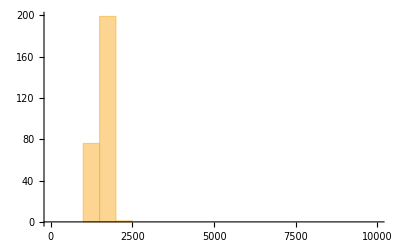

```mathematica
Histogram[{Select[Values@bubbleMeas,#[[2]]==0&][[All,1]],Select[Values@bubbleMeas,#[[2]]==1&][[All,1]]},{0,10000,500}]
```

## Number of corners of each domain

Use only internal bubbles not in contact with the boundary because those bubbles are not expected to have 6 corners.

```mathematica
boundaryDomains=DeleteDuplicates[Flatten[{#[[;;10]],#[[-10;;]],#[[All,;;10]],#[[All,-10;;]]}]]&/@bubbles;
```

```mathematica
internalBubbleInds=Complement[DeleteDuplicates[Flatten[bubbles[[#]]]],boundaryDomains[[#]]]&/@Range[Length@data];
```

```mathematica
cornerNumber=Flatten[Table[
Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,bubbles[[sim]],{2}]],DiskMatrix[1]]},
If[b==10,
-1(*that is the outside of the bubbles*),
Total@Flatten[ImageData[branchPoints[[sim]]]*ImageData[mask]]
]
],
{b,internalBubbleInds[[sim]]}],#>0&],
{sim,Length@data}],1];
```

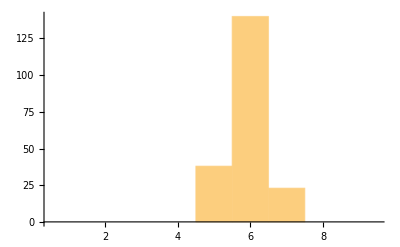

```mathematica
Histogram[cornerNumber,{0.5,10,1}]
```

```mathematica
Mean[cornerNumber]
```

5.92537

```mathematica
StandardDeviation[cornerNumber]
```

0.547177